```mathematica
lr
```

```mathematica
?life`*
```

updateLife[dim][stateXt]

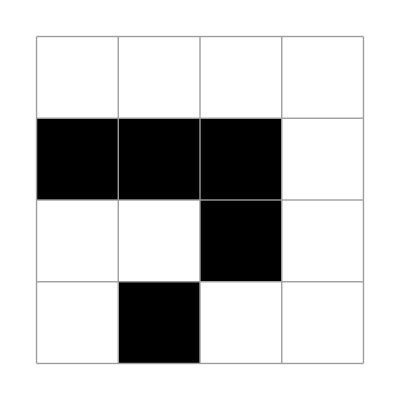
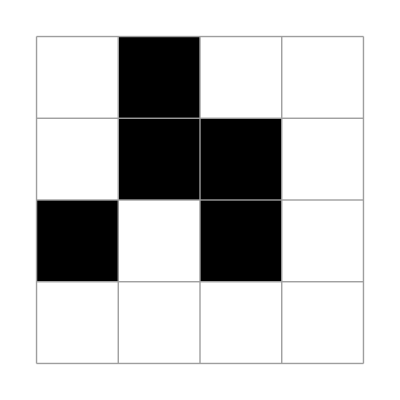
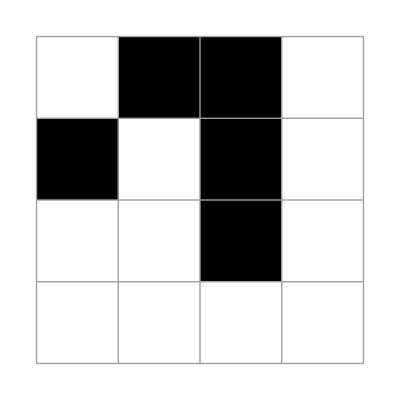
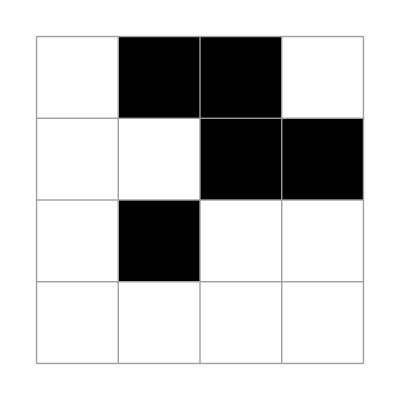

```mathematica
X1=({{0, 0, 0, 0}, {1, 1, 1, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}});
plt/@NestList[updateLife[{4,4}][ #]&,
X1,3]
```

```mathematica
X1=({{0, 0, 0, 0}, {1, 1, 1, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}});
plt/@NestList[updateLife[{4,4}][ #]&,
X1,3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
lr
```

```mathematica
life44
```

```mathematica
X1=({{0, 0, 0, 0}, {1, 1, 1, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}});
Plot3D[NestList[updateLife[{4,4}][ #]&,
X1,3] ]
```

Plot3D::argr: Plot3D called with 1 argument; 3 arguments are expected.

Plot3D[NestList[updateLife[{4,4}][#1]&,X1,3]]

so there are 65536 different initial states more than can be viewed by me in my lifetime